```mathematica
gT samp=10^(-2);(*sampling period*)
```

```mathematica
g f=10;(*frequency*)
```

```mathematica
x[t_]=Exp[I*2Pi*g f*t];(*continuous time wave*)
```

```mathematica
x d[t_]=x[Floor[t/gT samp]*gT samp];(*discretized wave*)
```

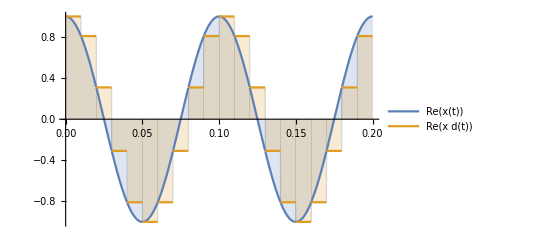

```mathematica
Plot[{Re[x[t]],Re[x d[t]]},{t,0,2/g f},Filling->Axis,PlotLegends->"Expressions"]
```

```mathematica
gN=200;gT int=gN*gT samp;(*Integration time*)
```

```mathematica
X[f_]=Integrate[x[t]*Exp[-I*2Pi*f*t],{t,0,gT int}]/gT int
```

(ⅈ-ⅈ ⅇ^(-4 ⅈ f π))/(2 (20 π-2 f π))

```mathematica
X d[f_]=(1-Exp[-I*2Pi*f*gT samp])/(I*2Pi*f)/gT int*Exp[I*2Pi*(g f-f)/2*(gN-1)*gT samp]*gN*Sinc[2Pi*(g f-f)/2*gN*gT samp]/Sinc[2Pi*(g f-f)/2*gT samp](*equals to Integrate[f d[t]*Exp[-I*2Pi*f*t],{t,0,gT int}]/gT int*)
```

-(50 ⅈ ⅇ^(199/100 ⅈ (10-f) π) (1-ⅇ^(-1/50 ⅈ f π)) Sinc[2 (10-f) π])/(f π Sinc[1/100 (10-f) π])

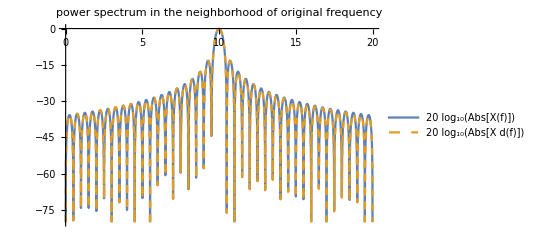

```mathematica
Plot[{20Log10[Abs[X[f]]],20Log10[Abs[X d[f]]]},{f,0,2g f},PlotRange->{-80,0},PlotStyle->{Default,Dashed},PlotLegends->"Expressions",PlotLabel->"power spectrum in the neighborhood of original frequency"]
```

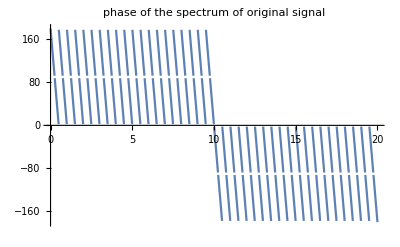

```mathematica
Plot[Arg[X[f]]/Degree,{f,0,2g f},PlotRange->Full,PlotLabel->"phase of the spectrum of original signal"]
```

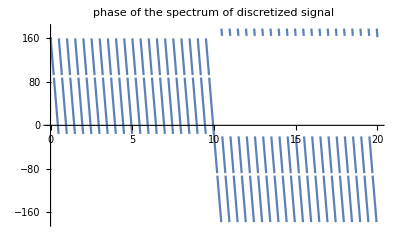

```mathematica
Plot[Arg[X d[f]]/Degree,{f,0,2g f},PlotRange->Full,PlotLabel->"phase of the spectrum of discretized signal"]
```

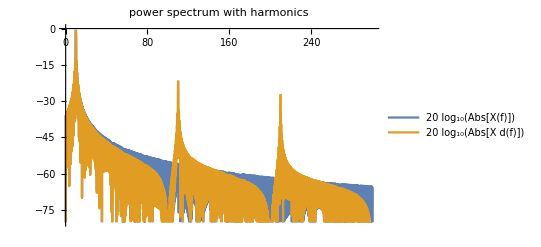

```mathematica
Plot[{20Log10[Abs[X[f]]],20Log10[Abs[X d[f]]]},{f,0,3/gT samp},PlotRange->{-80,0},PlotLegends->"Expressions",PlotLabel->"power spectrum with harmonics"]
```